```mathematica
i10={{10.500,10.000,{1.00,41.85,1.55}},{10.650,10.000,{0.97,43.13,0.72}},{10.800,10.000,{0.93,44.79,0.69}},{10.950,10.000,{0.00,46.43,0.58}},{11.100,10.000,{0.00,49.08,0.64}},{11.250,10.000,{1.00,53.05,2.03}},{11.400,10.000,{1.00,54.09,2.14}},{11.550,10.000,{1.00,55.80,2.29}},{11.700,10.000,{0.00,58.90,0.80}},{11.850,10.000,{1.00,59.91,2.45}},{12.000,10.000,{0.91,62.02,1.02}}};
```

```mathematica
SolveNi[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
nc=Min[ii[[All,2]]];
Assert[nc==Max[ii[[All,2]]]];
data={#[[1]],#[[3,1]]}&/@ii;
weights=1/(#[[3,2]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
ni=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[1]],Around[#[[3,1]],#[[3,2]]]}&/@ii,AxesLabel->{"Ni","Ions"},
PlotLabel->StringTemplate["Nc = `1`, Ni = `2` ± `3`"][nc,ni,err]],
Plot[lf[x],{x,Min[ii[[All,1]]-1],Max[ii[[All,1]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{ni,60},{ni,51}}],Line[{{ni-err,50},{ni+err,50}}]}
]];
{nc,Around[ni,err]}
]
```

```mathematica
SolveNiScf[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
nc=Min[ii[[All,2]]];
Assert[nc==Max[ii[[All,2]]]];
data={#[[1]],#[[3,2]]}&/@ii;
weights=1/(#[[3,3]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
ni=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[1]],Around[#[[3,2]],#[[3,3]]]}&/@ii,AxesLabel->{"Ni","Ions"},
PlotLabel->StringTemplate["Nc = `1`, Ni = `2` ± `3`"][nc,ni,err]],
Plot[lf[x],{x,Min[ii[[All,1]]-1],Max[ii[[All,1]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{ni,60},{ni,51}}],Line[{{ni-err,50},{ni+err,50}}]}
]];
{nc,Around[ni,err]}
]
```

```mathematica
SolveNc[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
ni=Min[ii[[All,1]]];
Assert[ni==Max[ii[[All,1]]]];
data={#[[2]],#[[3,1]]}&/@ii;
weights=1/(#[[3,2]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
nc=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[2]],Around[#[[3,1]],#[[3,2]]]}&/@ii,AxesLabel->{"Nc","Ions"},
PlotLabel->StringTemplate["Ni = `1`, Nc = `2` ± `3`"][ni,nc,err]],
Plot[lf[x],{x,Min[ii[[All,2]]-1],Max[ii[[All,2]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{nc,60},{nc,51}}],Line[{{nc-err,50},{nc+err,50}}]}
]];
{Around[nc,err],ni}
]
```

```mathematica
SolveNcScf[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
ni=Min[ii[[All,1]]];
Assert[ni==Max[ii[[All,1]]]];
data={#[[2]],#[[3,2]]}&/@ii;
weights=1/(#[[3,3]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
nc=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[2]],Around[#[[3,2]],#[[3,3]]]}&/@ii,AxesLabel->{"Nc","Ions"},
PlotLabel->StringTemplate["Ni = `1`, Nc = `2` ± `3`"][ni,nc,err]],
Plot[lf[x],{x,Min[ii[[All,2]]-1],Max[ii[[All,2]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{nc,60},{nc,51}}],Line[{{nc-err,50},{nc+err,50}}]}
]];
{Around[nc,err],ni}
]
```

```mathematica
i10
```

{{10.5,10.,{1.,41.85,1.55}},{10.65,10.,{0.97,43.13,0.72}},{10.8,10.,{0.93,44.79,0.69}},{10.95,10.,{0.,46.43,0.58}},{11.1,10.,{0.,49.08,0.64}},{11.25,10.,{1.,53.05,2.03}},{11.4,10.,{1.,54.09,2.14}},{11.55,10.,{1.,55.8,2.29}},{11.7,10.,{0.,58.9,0.8}},{11.85,10.,{1.,59.91,2.45}},{12.,10.,{0.91,62.02,1.02}}}

```mathematica
scfPaschenCurve={};
```

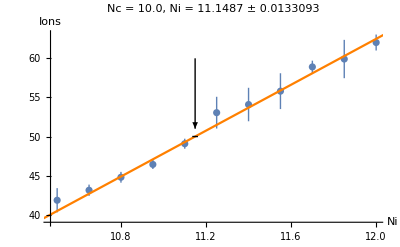

{10.,11.1490.013}

```mathematica
SolveNiScf[i10]
```

```mathematica
wbI10={{9.1,Around[27.73123127624291,1.4875870044572532]},{10.1,Around[43.25931684317911,2.2100015394421093]},{11.1,Around[49.23627355599849,2.812620697628194]},{12.1,Around[82.77825295914002,4.385041102859784]},{13.1,Around[90.64463798279338,9.377099149498877]}};
```

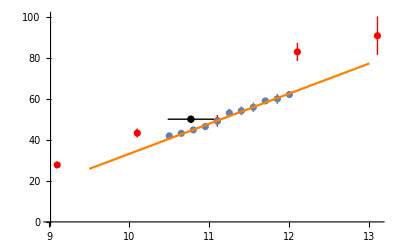

```mathematica
Show[ListPlot[{wbI10,{{Around[10.77,0.29],50}}},PlotStyle->{Red,Black}],-Graphics-]
```

```mathematica
i10rescan={{9.100,10.000,{1.00,27.39,0.81}},{9.500,10.000,{0.25,30.02,0.23}},{9.900,10.000,{0.00,34.00,0.39}},{10.300,10.000,{0.33,38.33,0.36}},{10.700,10.000,{1.00,44.01,1.63}},{11.100,10.000,{1.00,50.29,1.88}},{11.500,10.000,{0.37,54.23,0.56}},{11.900,10.000,{0.91,59.78,1.00}},{12.300,10.000,{0.97,67.79,1.31}},{12.700,10.000,{0.57,74.25,0.90}},{13.100,10.000,{0.99,83.45,2.71}}};
```

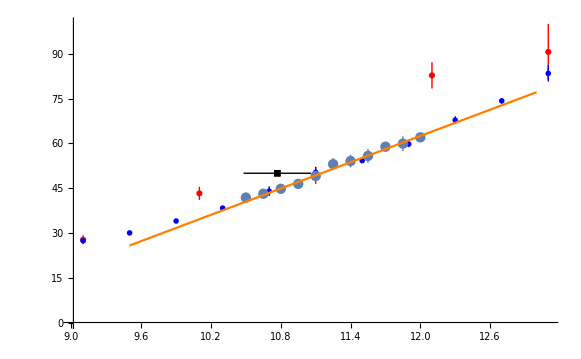

```mathematica
Show[ListPlot[{wbI10,{{Around[10.77,0.29],50}},{#[[1]],Around[#[[3,2]],#[[3,3]]]}&/@i10rescan},PlotStyle->{Red,Black,Blue},PlotMarkers->{Automatic,Automatic,"OpenMarkers"}],
-Graphics-]
```

```mathematica
i17={{10.500,17.800,{1.00,38.54,0.97}},{10.605,17.800,{0.00,39.73,0.34}},{10.710,17.800,{0.00,41.56,0.36}},{10.815,17.800,{0.00,44.28,0.38}},{10.920,17.800,{0.00,45.49,0.40}},{11.025,17.800,{0.00,47.37,0.42}},{11.130,17.800,{0.00,50.12,0.44}},{11.235,17.800,{0.00,52.94,0.46}},{11.340,17.800,{1.00,53.90,1.47}},{11.445,17.800,{0.00,57.71,0.51}},{11.550,17.800,{1.00,61.57,1.64}}};
```

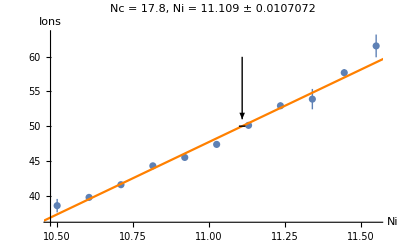

{17.8,11.1090.011}

```mathematica
SolveNiScf[i17]
```

```mathematica
wbI17={{9.1,Around[22.70370578052956,0.8766080525631543]},{10.1,Around[35.466903208885206,4.193671730634231]},{11.1,Around[52.58418996227591,6.131936144237329]},{12.1,Around[83.43231387455428,12.227862914277763]},{13.1,Around[120.80605979210428,4.909877000370364]}};
```

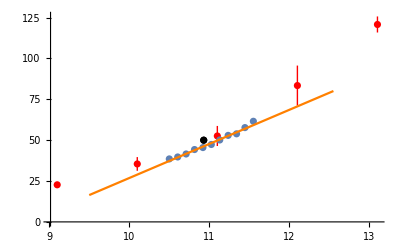

```mathematica
Show[ListPlot[{wbI17,{{Around[10.93,0.04],50}}},PlotStyle->{Red,Black}],-Graphics-]
```

```mathematica
i31={{12.520,31.600,{0.00,44.65,0.33}},{12.568,31.600,{0.00,45.53,0.34}},{12.616,31.600,{0.00,45.94,0.35}},{12.664,31.600,{0.00,47.29,0.36}},{12.712,31.600,{0.00,48.24,0.37}},{12.760,31.600,{0.00,48.97,0.38}},{12.808,31.600,{0.00,50.22,0.38}},{12.856,31.600,{0.00,52.62,0.40}},{12.904,31.600,{0.00,52.06,0.40}},{12.952,31.600,{0.00,54.19,0.41}},{13.000,31.600,{0.00,54.91,0.42}}};
```

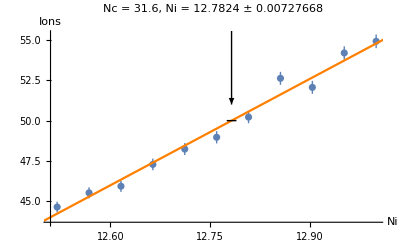

{31.6,12.7820.007}

```mathematica
SolveNiScf[i31]
```

```mathematica
i56={{15.600,56.200,{0.00,45.86,0.36}},{15.640,56.200,{1.00,47.73,1.15}},{15.680,56.200,{0.00,47.52,0.39}},{15.720,56.200,{0.00,48.69,0.40}},{15.760,56.200,{0.00,49.96,0.40}},{15.800,56.200,{0.00,50.46,0.40}},{15.840,56.200,{0.00,50.75,0.41}},{15.880,56.200,{0.00,53.30,0.42}},{15.920,56.200,{0.00,53.22,0.42}},{15.960,56.200,{0.13,53.09,0.31}},{16.000,56.200,{0.00,54.56,0.44}}};
```

```mathematica
i100={{20.000,100.000,{0.00,40.48,1.28}},{20.080,100.000,{0.00,43.11,1.36}},{20.160,100.000,{1.00,47.38,4.06}},{20.240,100.000,{0.00,45.18,1.34}},{20.320,100.000,{0.00,46.37,1.37}},{20.400,100.000,{0.00,46.80,1.43}},{20.480,100.000,{0.00,49.57,1.47}},{20.560,100.000,{0.00,50.45,1.54}},{20.640,100.000,{0.32,51.48,1.27}},{20.720,100.000,{0.00,56.45,1.72}},{20.800,100.000,{0.28,54.70,1.23}}};
```

```mathematica
i178={{27.600,178.000,{0.22,43.01,0.61}},{27.660,178.000,{0.32,44.81,0.73}},{27.720,178.000,{0.00,46.13,0.98}},{27.780,178.000,{0.00,47.62,0.96}},{27.840,178.000,{0.00,46.14,1.01}},{27.900,178.000,{0.00,48.23,1.00}},{27.960,178.000,{0.00,49.24,1.04}},{28.020,178.000,{0.00,50.26,1.07}},{28.080,178.000,{0.00,50.96,1.07}},{28.140,178.000,{0.06,51.17,0.99}},{28.200,178.000,{0.00,53.45,1.11}}};
```

```mathematica
i316={{38.100,316.000,{0.81,33.82,2.81}},{38.575,316.000,{1.00,41.69,11.24}},{39.050,316.000,{0.25,46.20,2.26}},{39.525,316.000,{0.33,52.27,3.32}},{40.000,316.000,{0.35,53.35,3.52}}};
```

```mathematica
(* Max Ni 39.280 Nc 316.000 z 0.00 ions 44.84 error 0.88 *)
i316={{39.000,316.000,{0.00,41.79,1.04}},{39.2,316.0,{0,43.55,0.86}},{39.250,316.000,{0.18,43.45,0.72}},
{39.28,316.0,{0.00,44.84,.88}},
{39.500,316.000,{1.00,48.92,3.50}},{39.750,316.000,{0.00,52.01,1.27}},{40.000,316.000,{0.00,55.33,1.43}}};
```

```mathematica
i316={{39.200,316.000,{0.00,43.55,0.86}},{39.280,316.000,{0.00,44.84,0.88}},{39.360,316.000,{0.21,45.21,0.57}},{39.440,316.000,{0.00,48.76,0.90}},{39.520,316.000,{0.00,48.09,0.92}},{39.600,316.000,{0.00,49.08,0.98}},{39.680,316.000,{0.00,50.28,1.00}},{39.760,316.000,{0.00,49.61,0.96}},{39.840,316.000,{0.00,53.05,1.02}},{39.920,316.000,{0.15,53.64,0.71}},{40.000,316.000,{0.00,55.35,1.06}}};
```

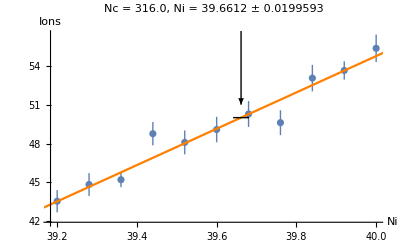

{316.,39.6610.020}

```mathematica
SolveNiScf[i316]
```

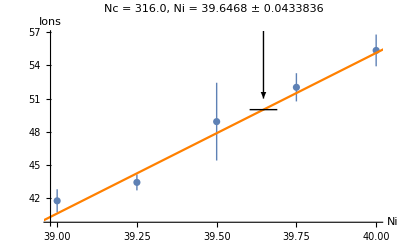

{316.,39.650.04}

```mathematica
SolveNiScf[i316]
```

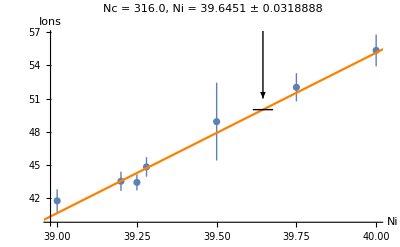

{316.,39.6450.032}

```mathematica
SolveNiScf[i316]
```

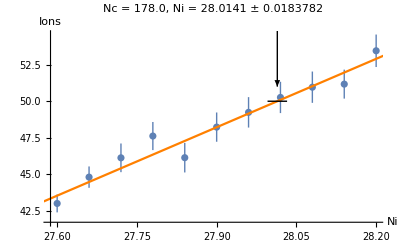

{178.,28.0140.018}

```mathematica
SolveNiScf[i178]
```

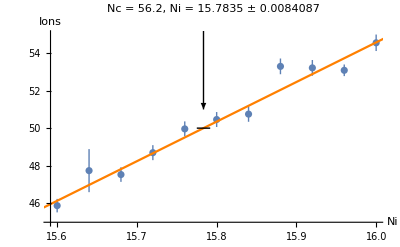

{56.2,15.7840.008}

```mathematica
SolveNiScf[i56]
```

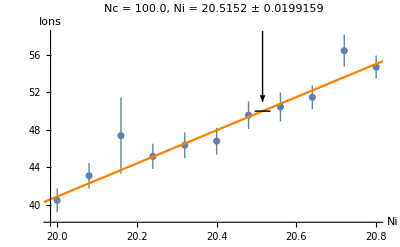

{100.,20.5150.020}

```mathematica
SolveNiScf[i100]
```

```mathematica
c20={{20.000,4.300,{0.73,46.93,0.71}},{20.000,4.330,{0.73,46.60,0.71}},{20.000,4.360,{0.73,47.94,0.73}},{20.000,4.390,{0.73,47.96,0.76}},{20.000,4.420,{0.73,48.16,0.76}},{20.000,4.450,{0.71,49.86,0.76}},{20.000,4.480,{0.72,50.93,0.78}},{20.000,4.510,{0.72,51.58,0.77}},{20.000,4.540,{0.73,54.10,0.81}},{20.000,4.570,{0.75,54.96,0.86}},{20.000,4.600,{0.72,53.18,0.82}}};
```

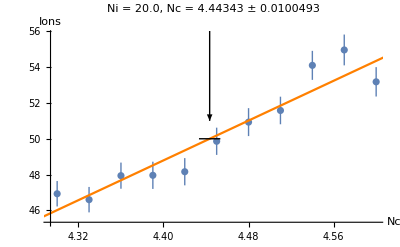

{4.4430.010,20.}

```mathematica
SolveNcScf[c20]
```

```mathematica
c15={{15.000,5.200,{0.74,45.12,0.67}},{15.000,5.260,{0.75,46.04,0.71}},{15.000,5.320,{0.73,48.49,0.69}},{15.000,5.380,{0.74,48.40,0.73}},{15.000,5.440,{0.72,48.51,0.70}},{15.000,5.500,{0.73,50.19,0.75}},{15.000,5.560,{0.71,51.73,0.71}},{15.000,5.620,{0.75,53.17,0.82}},{15.000,5.680,{0.71,54.13,0.78}},{15.000,5.740,{0.74,53.77,0.81}},{15.000,5.800,{0.72,57.33,0.80}}};
```

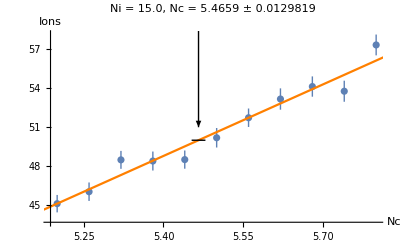

{5.4660.013,15.}

```mathematica
SolveNcScf[c15]
```

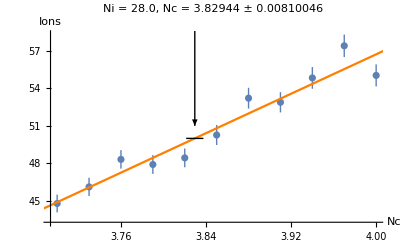

{3.8290.008,28.}

```mathematica
SolveNcScf[c28]
```

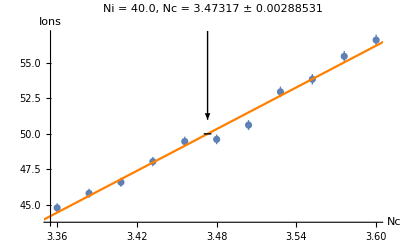

{3.47320.0029,40.}

```mathematica
SolveNcScf[c40]
```

```mathematica
c28={{28.000,3.700,{0.73,44.79,0.71}},{28.000,3.730,{0.74,46.12,0.73}},{28.000,3.760,{0.74,48.32,0.74}},{28.000,3.790,{0.74,47.91,0.75}},{28.000,3.820,{0.72,48.44,0.75}},{28.000,3.850,{0.73,50.27,0.80}},{28.000,3.880,{0.73,53.22,0.83}},{28.000,3.910,{0.73,52.89,0.81}},{28.000,3.940,{0.74,54.84,0.87}},{28.000,3.970,{0.74,57.41,0.90}},{28.000,4.000,{0.73,55.04,0.88}}};
```

```mathematica
c40={{40.000,3.360,{0.73,44.77,0.32}},{40.000,3.384,{0.73,45.80,0.32}},{40.000,3.408,{0.72,46.58,0.32}},{40.000,3.432,{0.73,48.04,0.33}},{40.000,3.456,{0.73,49.46,0.34}},{40.000,3.480,{0.73,49.61,0.34}},{40.000,3.504,{0.73,50.62,0.35}},{40.000,3.528,{0.73,52.97,0.37}},{40.000,3.552,{0.73,53.86,0.37}},{40.000,3.576,{0.73,55.48,0.38}},{40.000,3.600,{0.73,56.63,0.39}}};
```

```mathematica
scfPaschenCurve={{3.47320.0029,40.},{3.8290.008,28.},{5.4660.013,15.},{4.4430.010,20.},{10.,11.1490.013},{17.8,11.1090.011},{31.6,12.7820.007},{56.2,15.7840.008},{100.,20.5150.020}};
```

```mathematica
AppendTo[scfPaschenCurve,%]
```

{{3.47320.0029,40.},{3.8290.008,28.},{5.4660.013,15.},{4.4430.010,20.},{10.,11.1490.013},{17.8,11.1090.011},{31.6,12.7820.007},{56.2,15.7840.008},{100.,20.5150.020},{178.,28.0140.018},{316.,39.6610.020}}

```mathematica
PrependTo[scfPaschenCurve,%]
```

{{3.47320.0029,40.},{3.8290.008,28.},{5.4660.013,15.},{4.4430.010,20.},{10.,11.1490.013},{17.8,11.1090.011},{31.6,12.7820.007},{56.2,15.7840.008}}

```mathematica
paschenCurve={{4.0320.006,100.},{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025},{178.,27.800.05},{316.,39.460.04},{562.,57.980.07},{1000.,87.650.12}};
```

```mathematica
paschenCurveLV={#[[1]]/5,15#[[2]]}&/@paschenCurve
```

{{0.80630.0012,1500.},{1.2990.004,225.},{1.09370.0034,300.},{2,168.410.12},{3.56,165.390.14},{6.32,189.540.10},{11.24,233.370.29},{20.,305.20.4},{35.6,417.10.8},{63.2,591.80.6},{112.4,869.71.1},{200.,1314.81.8}}

```mathematica
scfPaschenCurveLV={#[[1]]/5.3,15#[[2]]}&/@scfPaschenCurve
```

{{0.65530.0005,600.},{0.72250.0015,420.},{1.03130.0024,225.},{0.83840.0019,300.},{1.88679,167.230.20},{3.35849,166.630.16},{5.96226,191.740.11},{10.6038,236.750.13},{18.8679,307.730.30},{33.5849,420.210.28},{59.6226,594.920.30}}

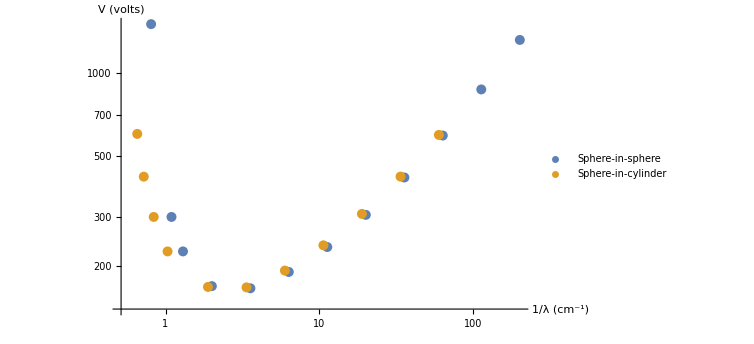

```mathematica
ListLogLogPlot[{paschenCurveLV,scfPaschenCurveLV},AxesLabel->{"1/λ (cm^-1)","V (volts)"},PlotLegends->{"Sphere-in-sphere","Sphere-in-cylinder"}]
```

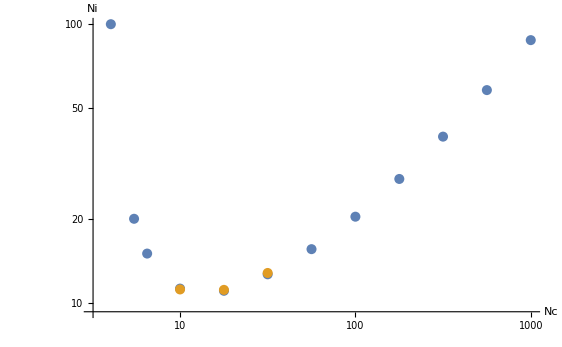

```mathematica
ListLogLogPlot[{paschenCurve,scfPaschenCurve},AxesLabel->{"Nc","Ni"}]
```

```mathematica
Sort[paschenCurve,#1[[1]]<#2[[1]]&]
```

{{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025}}

```mathematica
cwCs1=Total[(cwNlf1["FitResiduals"]/(#[[3,2]]&/@cwVals1))^2]
```

12.5973

```mathematica
ExpFitter[vals_]:=Module[{nlf,chiSquare},
nlf=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@vals,p1 Exp[p2 x]+p3,{p1,p2,p3},x,Weights->((1/(#[[2,2]])^2)&/@vals)];
Print[nlf];
Print[Show[ListPlot[{#[[1]],Around[#[[2,1]],#[[2,2]]]}&/@vals],Plot[nlf[x],{x,3,5}]]];
chiSquare=Total[(nlf["FitResiduals"]/(#[[2,2]]&/@vals))^2];
Print["Χ^2 = ",chiSquare];
nlf
];
```

FittedModel[-4.4034+1.7674 ⅇ^(0.852934 x)]

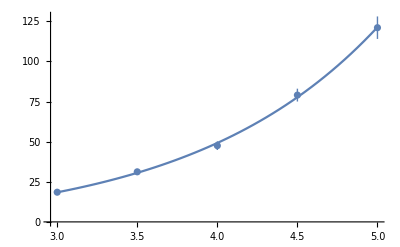

Χ^2 = 0.622512

```mathematica
ExpFitter[vals];
```

FittedModel[-3.28487+1.60157 ⅇ^(0.871451 x)]

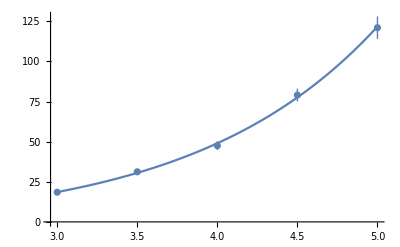

Χ^2 = 0.593408

```mathematica
ExpFitter[vals];
```

FittedModel[13.9946+0.179058 ⅇ^(1.28162 x)]

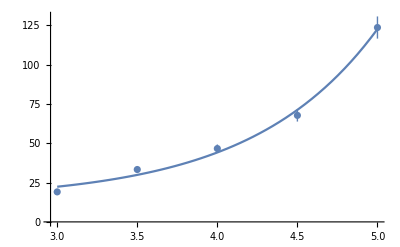

Χ^2 = 12.5973

```mathematica
ExpFitter[cwVals1[[All,2;;3]]];
```

FittedModel[2.18802+1.08588 ⅇ^(0.930871 x)]

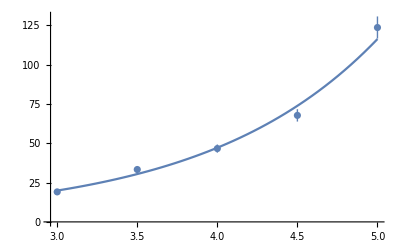

Χ^2 = 6.56454

```mathematica
ExpFitter[cwVals1[[All,2;;3]]];
```

```mathematica
cwVals1
```

{{100.,3.,{19.08,1.22}},{100.,3.5,{33.3,1.8}},{100.,4.,{46.62,2.58}},{100.,4.5,{67.71,3.92}},{100.,5.,{123.56,7.04}}}

```mathematica
cwVals1={{100.,3.,{19.08,1.22}},{100.,3.5,{33.3,1.8}},{100.,4.,{46.62,2.58}},{100.,4.5,{67.71,3.92}},{100.,5.,{123.56,7.04}}};
```

```mathematica
cwVals2={{100.000,3.000,{19.24,1.09}},{100.000,3.500,{29.72,1.75}},{100.000,4.000,{49.62,3.07}},{100.000,4.500,{82.67,4.52}},{100.000,5.000,{123.60,7.33}}};
```

FittedModel[-9.15922+2.47759 ⅇ^(0.797318 x)]

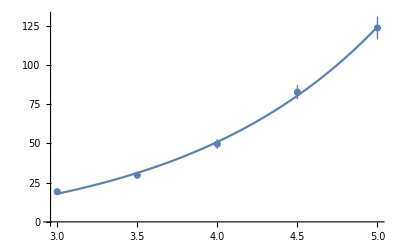

Χ^2 = 2.60626

```mathematica
ExpFitter[cwVals2[[All,2;;3]]];
```

FittedModel[-0.876236+1.21828 ⅇ^(0.930419 x)]

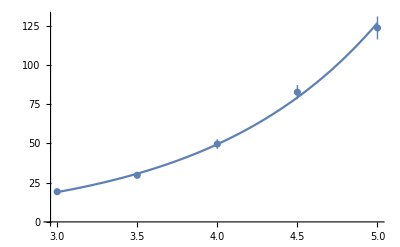

Χ^2 = 1.14659

```mathematica
ExpFitter[cwVals2[[All,2;;3]]];
```

```mathematica
cwVals3={{100.000,3.000,{17.71,1.00}},{100.000,3.500,{27.44,1.63}},{100.000,4.000,{47.25,3.16}},{100.000,4.500,{78.48,4.64}},{100.000,5.000,{129.88,7.11}}};
```

FittedModel[0.249599+0.793574 ⅇ^(1.01936 x)]

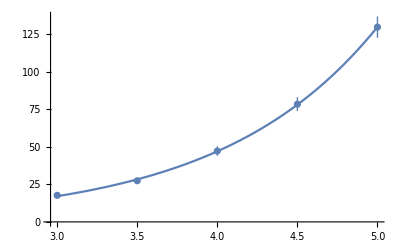

Χ^2 = 0.656764

```mathematica
ExpFitter[cwVals3[[All,2;;3]]];
```

FittedModel[2.73749+0.581989 ⅇ^(1.07906 x)]

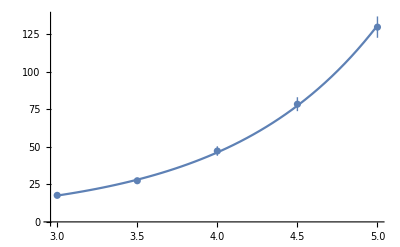

Χ^2 = 0.36799

```mathematica
ExpFitter[cwVals3[[All,2;;3]]];
```

```mathematica
cwVals4={{100.000,3.000,{17.36,0.97}},{100.000,3.500,{28.86,1.85}},{100.000,4.000,{46.99,2.40}},{100.000,4.500,{73.15,4.23}},{100.000,5.000,{123.75,7.09}}};
```

FittedModel[2.97084+0.673892 ⅇ^(1.03706 x)]

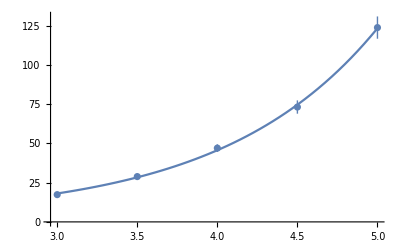

Χ^2 = 1.08932

```mathematica
ExpFitter[cwVals4[[All,2;;3]]];
```

FittedModel[-0.809542+1.04612 ⅇ^(0.952935 x)]

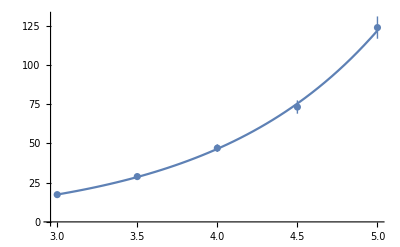

Χ^2 = 0.418961

```mathematica
ExpFitter[cwVals4[[All,2;;3]]];
```

```mathematica
cwVals5={{100.000,3.000,{18.20,0.35}},{100.000,3.500,{30.34,0.54}},{100.000,4.000,{48.22,0.88}},{100.000,4.500,{76.87,1.41}},{100.000,5.000,{121.15,2.24}}};
```

FittedModel[-2.84486+1.49279 ⅇ^(0.883906 x)]

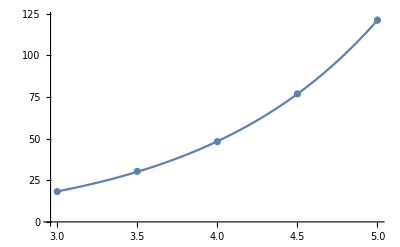

Χ^2 = 0.379302

```mathematica
ExpFitter[cwVals5[[All,2;;3]]];
```

FittedModel[-3.48668+1.58657 ⅇ^(0.872396 x)]

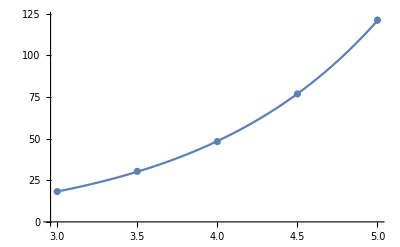

Χ^2 = 0.291491

```mathematica
ExpFitter[cwVals5[[All,2;;3]]];
```

```mathematica
cwVals6={{100.000,3.000,{18.31,0.34}},{100.000,3.500,{29.58,0.54}},{100.000,4.000,{48.75,0.87}},{100.000,4.500,{78.93,1.45}},{100.000,5.000,{122.09,2.22}}};
```

FittedModel[-5.82703+1.86682 ⅇ^(0.84582 x)]

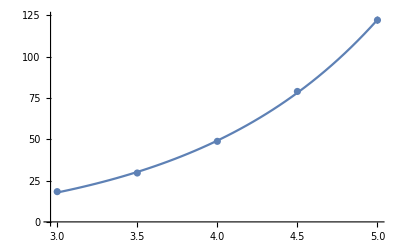

Χ^2 = 4.32461

```mathematica
ExpFitter[cwVals6[[All,2;;3]]];
```

FittedModel[-2.60814+1.39897 ⅇ^(0.899907 x)]

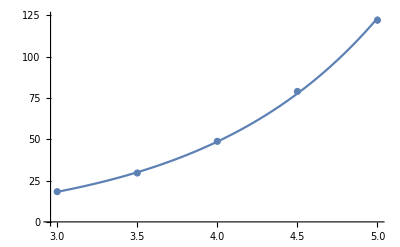

Χ^2 = 1.88155

```mathematica
ExpFitter[cwVals6[[All,2;;3]]];
```